## Part 1 - Recap

In the last simulation, we simulated a hypothetical universe with a gravitational constant of 100 Newtons times square meter per kilogram (N*m^2/kg). We had a star with a mass of 50 kilograms, a planet with a mass of 0.1 grams (0.0001 kilograms) in orbit around the star, and a moon in orbit around the planet with a mass of 2 milligrams (0.000002 kilograms). The star stayed close to the origin the entire time, the planet orbited the star at a distance of 50 meters, and the moon orbited the planet at a distance of 10 centimeters (0.10 meters).

## Part 2 - Defining the Variables

This time, we are going to use the real-life gravitational constant (G = 6.6743*10^-11 N*m^2/kg) and replace the star-planet-moon system with the system of the Sun, our home planet Earth, and Earth’s Moon. Because seconds are useless for long orbital periods like the Moon’s orbit and Earth’s orbit, we’ll convert the gravitational constant from seconds (in which the base units of G are m^3*kg^-1*s^-2). The masses of the Sun, Earth, and the Moon are m1, m2, and m3, respectively, and their respective distances from the origin are r1, r2, and r3. This time, the Moon will orbit Earth in the same direction as Earth will orbit the Sun unlike in the previous simulation in which the moon orbited in the opposite direction that the planet did the star.

```mathematica
ConvertSecondstoDays[t_]:=t/(60*60*24)

G=6.6743*10^-11/(ConvertSecondstoDays[1])^2

m1=1.9885*10^30
m2=5.9722*10^24
m3=7.346*10^22

r1i={0,0};
r2i={1.496*10^11,0};
r3i={3.84399*10^8,0};

r1i//MatrixForm
r2i//MatrixForm
r3i//MatrixForm
```

0.498234

1.9885×10^30

5.9722×10^24

7.346×10^22

(0
0)

(1.496×10^11
0)

(3.84399×10^8
0)

## Part 3 - Defining the Functions and Diff. Equations

```mathematica
r1[t_]:={x1[t],y1[t]}
r2[t_]:={x2[t],y2[t]}
r3[t_]:={x3[t],y3[t]}

r12[t_]:=r2[t]-r1[t]
r13[t_]:=r3[t]-r1[t]

r21[t_]:=r1[t]-r2[t]
r23[t_]:=r3[t]-r2[t]

r31[t_]:=r1[t]-r3[t]
r32[t_]:=r2[t]-r3[t]

acc1[t_]:={G*m2*Normalize[r12[t]][[1]]/(Norm[r12[t]])^2,G*m2*Normalize[r12[t]][[2]]/(Norm[r12[t]])^2}+{G*m3*Normalize[r13[t]][[1]]/(Norm[r13[t]])^2,G*m3*Normalize[r13[t]][[2]]/(Norm[r13[t]])^2}
acc2[t_]:={G*m1*Normalize[r21[t]][[1]]/(Norm[r21[t]])^2,G*m1*Normalize[r21[t]][[2]]/(Norm[r21[t]])^2}+{G*m3*Normalize[r23[t]][[1]]/(Norm[r23[t]])^2,G*m3*Normalize[r23[t]][[2]]/(Norm[r23[t]])^2}
acc3[t_]:={G*m1*Normalize[r31[t]][[1]]/(Norm[r31[t]])^2,G*m1*Normalize[r31[t]][[2]]/(Norm[r31[t]])^2}+{G*m2*Normalize[r32[t]][[1]]/(Norm[r32[t]])^2,G*m2*Normalize[r32[t]][[2]]/(Norm[r32[t]])^2}
```

## Part 4 - Setting Up the Initial Acc. and Velocities

```mathematica
acc1i={0,0};
acc2i={G*m1*Normalize[r2i][[1]]/Norm[r2i]^2,G*m1*Normalize[r2i][[2]]/Norm[r2i]^2};
acc3i={G*m2*Normalize[r3i][[1]]/Norm[r3i]^2,G*m2*Normalize[r3i][[2]]/Norm[r3i]^2};

v1i={0,0};
v2i={0,Sqrt[Norm[r2i]*Norm[acc2i]]};
v3i={0,Sqrt[Norm[r3i]*Norm[acc3i]]}+v2i;

v1i//MatrixForm
v2i//MatrixForm
v3i//MatrixForm
```

(0
0)

(0
2.57344×10^9)

(0
2.66142×10^9)

## Part 5 - Solving the Differential Equation

```mathematica
solution=NDSolve[{x1''[t]==acc1[t][[1]],y1''[t]==acc1[t][[2]],x2''[t]==acc2[t][[1]],y2''[t]==acc2[t][[2]],x3''[t]==acc3[t][[1]],y3''[t]==acc3[t][[2]],x1[0]==r1i[[1]],y1[0]==r1i[[2]],x2[0]==r2i[[1]],y2[0]==r2i[[2]],x3[0]==r2i[[1]]+r3i[[1]],y3[0]==r2i[[2]]+r3i[[2]],x1'[0]==v1i[[1]],y1'[0]==v1i[[2]],x2'[0]==v2i[[1]],y2'[0]==v2i[[2]],x3'[0]==v3i[[1]],y3'[0]==v3i[[2]]},{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]},{t,0,1000}];

x1sol=x1[t]/.solution[[1]];
y1sol=y1[t]/.solution[[1]];

x2sol=x2[t]/.solution[[1]];
y2sol=y2[t]/.solution[[1]];

x3sol=x3[t]/.solution[[1]];
y3sol=y3[t]/.solution[[1]];
```

## Part 6 - Graphing the Results

Just like we did with the last simulation, we’ll plot the orbital motion of the Sun, Earth, and the Moon.

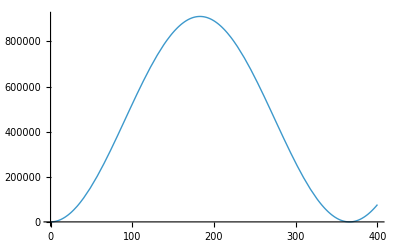

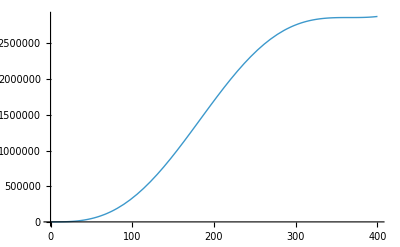

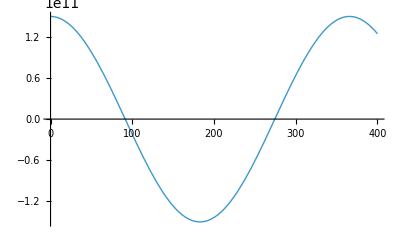

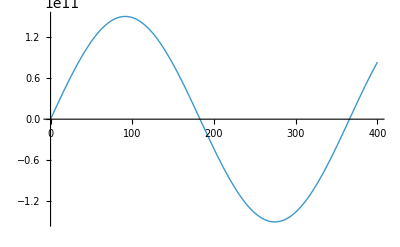

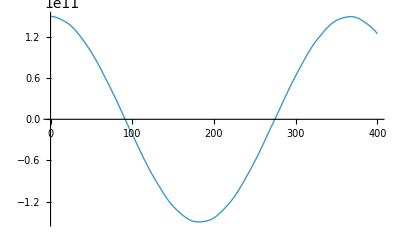

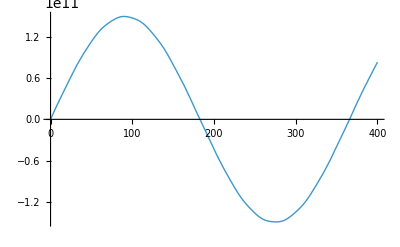

```mathematica
Plot[x1sol,{t,0,400},PlotStyle->Thick,PlotRange->All]
Plot[y1sol,{t,0,400},PlotStyle->Thick,PlotRange->All]

Plot[x2sol,{t,0,400},PlotStyle->Thick,PlotRange->All]
Plot[y2sol,{t,0,400},PlotStyle->Thick,PlotRange->All]

Plot[x3sol,{t,0,400},PlotStyle->Thick,PlotRange->All]
Plot[y3sol,{t,0,400},PlotStyle->Thick,PlotRange->All]
```

You can see how the Sun is also moved a fair bit by the gravitational influence of Earth and the Moon in this simulation. In real life, the other objects in the Solar System actually make the Sun orbit around what is called the “barycenter.” The real-life distance between the Sun and the barycenter is about 1 million kilometers at the maximum, about 1.4 times the Sun’s radius. Now let’s subtract Earth’s motion with respect to the Sun from the Moon’s motion with respect to the Sun to get the Moon’s motion with respect to Earth.

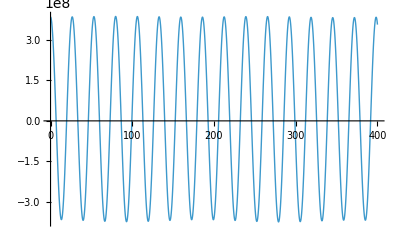

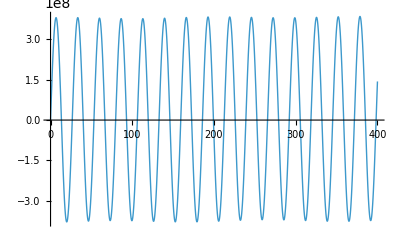

```mathematica
Plot[x3sol-x2sol,{t,0,400},PlotStyle->Thick,PlotRange->All]
Plot[y3sol-y2sol,{t,0,400},PlotStyle->Thick,PlotRange->All]
```

Of course, we’ll need to shorten the x-ranges of both graphs so that we can see much clearer the Moon’s orbital motion.

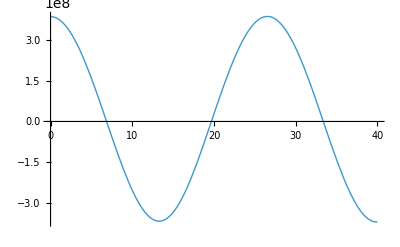

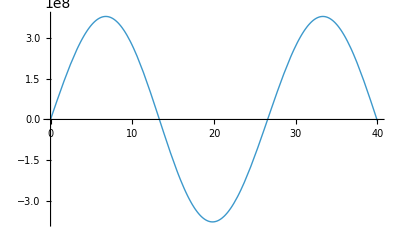

```mathematica
Plot[x3sol-x2sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[y3sol-y2sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
```

## Part 7 - Double-Checking the Results

Like we did in the last simulation with the hypothetical planet and its hypothetical moon, we’ll find the orbital periods of Earth and the Moon and compare the resulting trigonometric functions to the generated motion from the differential equations. Let’s first compute the orbital periods of both bodies (remember, they are measured in days):

```mathematica
T2=Sqrt[4*Pi^2*(Norm[r2i])^3/(G*(m1+m2))]
T3=Sqrt[4*Pi^2*(Norm[r3i])^3/(G*(m2+m3))]
```

365.256

27.2844

Now let’s graph Earth’s calculated orbit alongside its predicted orbit.

0.00273781

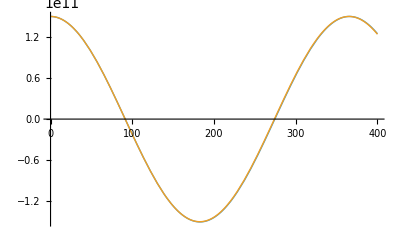

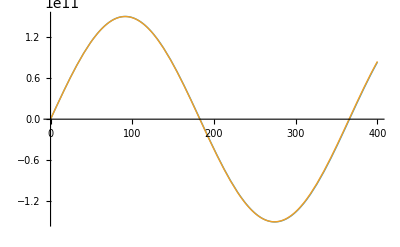

```mathematica
f2=1/T2

Plot[{x2sol,Norm[r2i]*Cos[2*Pi*f2*t]},{t,0,400},PlotStyle->Thick,PlotRange->All]
Plot[{y2sol,Norm[r2i]*Sin[2*Pi*f2*t]},{t,0,400},PlotStyle->Thick,PlotRange->All]
```

Now let’s do the same with the orbital motion of the Moon with respect to Earth:

0.0366509

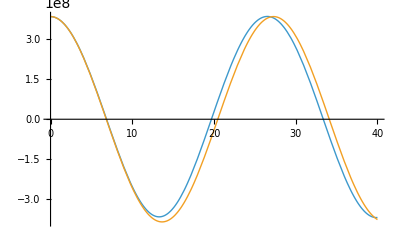

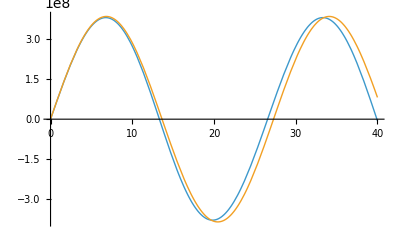

```mathematica
f3=1/T3

Plot[{x3sol-x2sol,Norm[r3i]*Cos[2*Pi*f3*t]},{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[{y3sol-y2sol,Norm[r3i]*Sin[2*Pi*f3*t]},{t,0,40},PlotStyle->Thick,PlotRange->All]
```

Like with the last simulation in which the moon’s orbital period had a greater error than the planet, the orbital period of Earth’s Moon has a greater error in this simulation than that of Earth itself. Also, let’s find the percent error of the orbital periods of Earth and the Moon comparing what we predicted to the actual values in real life. We’ll measure the errors in percentage from the real-life values.

```mathematica
T2Real=365.256363004
T3Real=27.321661

Error2=100*Abs[T2Real-T2]/T2Real
Error3=100*Abs[T3Real-T3]/T3Real
```

365.256

27.3217

0.000134898

0.136294